```mathematica
Clear["Global`*"]
f[x_,y_] := μ*x+y-x^2;
g[x_,y_] := -x+μ*y+2x^2;
sol = Solve[f[x,y]==0 && g[x,y]==0, {x,y}]
J[x_,y_]:= {{D[f[x,y],x], D[f[x,y],y]}, {D[g[x,y],x], D[g[x,y],y]}};
μ=0;
J[x,y]/.x->0//MatrixForm
eval =J[x,y]/.sol[[2]] // Eigenvalues
evec = J[x,y]/.sol[[2]] // Eigenvectors;
```

{{x→0,y→0},{x→(1+μ^2)/(2+μ),y→(1-2 μ+μ^2-2 μ^3)/(2+μ)^2}}

(0 | 1
-1 | 0)

{1/2 (-1-√5),1/2 (-1+√5)}

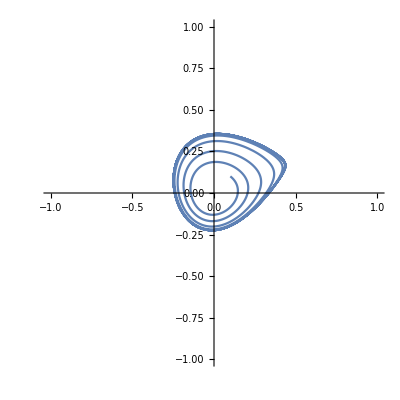

```mathematica
s=NDSolve[{x'[t]==μ*x[t]+y[t]-x[t]^2,y'[t]==-x[t]+μ*y[t]+2 x[t]^2,x[0]==y[0]==0.1}/.μ->0.060,{x,y},{t,0,100}];
ParametricPlot[Evaluate[{x[t],y[t]}/. s],{t,0,100},PlotRange->{{-1,1},{-1,1}}]
```

```mathematica
s=.
sol=DSolve[{x'[t]==u*x[t], y'[t]==s*y[t], x[0]==γ, y[0]==1},{x[t], y[t]},t] //Flatten
```

{x[t]→ⅇ^(t u) γ,y[t]→ⅇ^(s t)}

```mathematica
Solve[x[t]==1/.sol, t]
```

```mathematica
{{t->ConditionalExpression[(2 ⅈ π C[1]+Log[1/γ])/u, C[1]∈Integers]}}
```

{{t→ConditionalExpression[(2 ⅈ π C[1]+Log[1/γ])/u, C[1]∈ℤ]}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

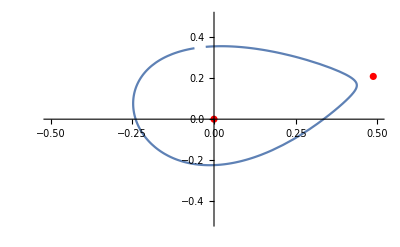

```mathematica
Clear["Global`*"]
μc = 0.066;
f[x_,y_]:=μ x + y -x^2 ;
g[x_,y_]:=-x + μ y +2x^2 ;
μ = 0.060;
tMin = 165;
tMax = tMin+9.8624007122786-0.1;
fp = Solve[{f[x,y]==0, g[x,y]==0}, {x,y}];
data={{fp[[1,1,2]],fp[[1,2,2]]},{fp[[2,1,2]],fp[[2,2,2]]}};
line =  Fit[data,{1,x},x];
p1 = ListPlot[data,PlotStyle->Red];
s=NDSolve[{x'[t]==μ*x[t]+y[t]-x[t]^2,y'[t]==-x[t]+μ*y[t]+2 x[t]^2,x[0]==y[0]==0.1},{x,y},{t,tMin,tMax}];
p3= ParametricPlot[Evaluate[{x[t],y[t]}/. s],{t,tMin,tMax},PlotRange->{{-1,1},{-1,1}}] ;
Show[p1,p3,PlotRange->{{-0.5,0.5},{-0.5,0.5}}]
```

```mathematica
(*μ, γ*)
tIntersect = Solve[{y[t]==fp[[2,2,2]]}/.s[[1,2]],t][[1,1,2]];
xIf = s[[1,1,2]];

γ = xIf[tIntersect](* x intersect *)
xVal = Log[Abs[μ-μc]]
yVal = Log[γ]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

InterpolatingFunction::dmval: Input value {164.312} lies outside the range of data in the interpolating function. Extrapolation will be used.

-0.21211

-5.116

-1.55065+3.14159 ⅈ

2.78486+0.690574 x

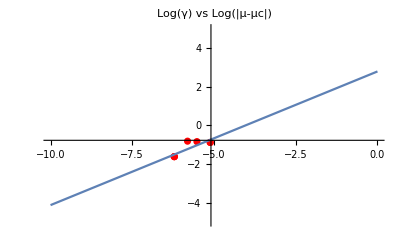

```mathematica
plotData = {{-5.115995809754081,-0.8831824175751058},{-5.115995809754081, -0.8831824175751058},{-5.521460917862245,-0.8397348233958074},{-5.809142990314027,-0.8169247714703272},{-6.2146080984221905,-1.6161665232963962},{-6.2146080984221905,-1.6161665232963962},{-6.2146080984221905,-1.6161665232963962}};
line =  Fit[plotData,{1,x},x]
gammaPlot = Show[ListPlot[plotData,PlotStyle->Red],Plot[line,{x,-10,0}],PlotRange->{{-10,0},{-5,5}}, PlotLabel->"Log(γ) vs Log(|μ-μc|)"]
```

```mathematica
(* b *)
Clear["Global`*"]
μc = 0.066;
f[x_,y_] := μ*x+y-x^2;
g[x_,y_] := -x+μ*y+2x^2;
sol = Solve[f[x,y]==0 && g[x,y]==0, {x,y}];
```

-1

{{x→0,y→0},{x→2,y→6}}

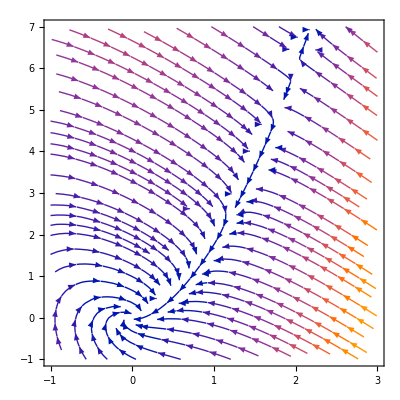

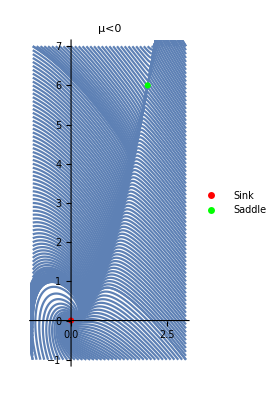

```mathematica
μ=-1
sol = Solve[f[x,y]==0 && g[x,y]==0, {x,y}]
StreamPlot[{f[x,y], g[x,y]}, {x,-1,3}, {y,-1,7}]
minx=-1; maxx=3; miny=-1;  maxy=7;
s[x0_,y0_]:=NDSolve[{x'[t]==μ*x[t]+y[t]-x[t]^2,y'[t]==-x[t]+μ*y[t]+2 x[t]^2,x[0]==x0, y[0]==y0},{x,y},{t,0,10}];
initialCondition=Join[Table[{minx,y},{y,miny,maxy,0.1}],Table[{maxx,y},{y,miny,maxy,0.1}],Table[{x,miny},{x,minx,maxx,0.1}],Table[{x,maxy},{x,minx,maxx,0.1}]];
Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/. s[initialCondition[[i,1]],initialCondition[[i,2]]]],{t,0,10}, PlotRange->{{minx,maxx},{miny,maxy}}],{i,Length[initialCondition]}], ListPlot[{{0,0}}, PlotStyle->{Red}, PlotMarkers->{Automatic, 6},PlotLegends->{"Sink"}], ListPlot[{{sol[[2,1,2]],sol[[2,2,2]]}}, PlotStyle->{Green}, PlotMarkers->{Automatic, 6},PlotLegends->{"Saddle"}],PlotLabel-> "μ<0"]
```

0

{{x→0,y→0},{x→1/2,y→1/4}}

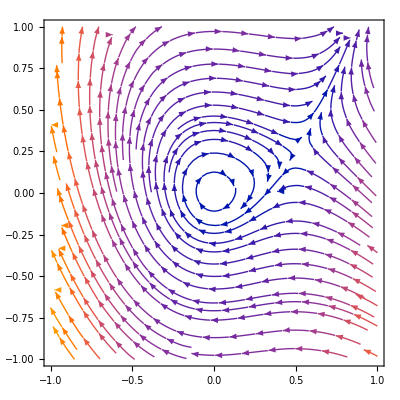

NDSolve::nderr: Error test failure at t == 25.1214; unable to continue.

NDSolve::nderr: Error test failure at t == 25.218; unable to continue.

NDSolve::nderr: Error test failure at t == 25.3038; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

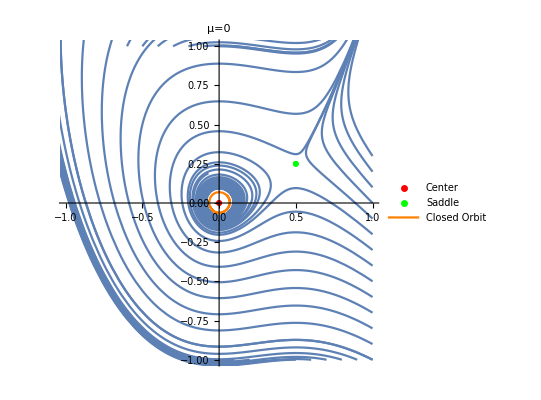

```mathematica
μ=0
sol = Solve[f[x,y]==0 && g[x,y]==0, {x,y}]
StreamPlot[{f[x,y], g[x,y]}, {x,-1,1}, {y,-1,1}]
minx=-1; maxx=1; miny=-1;  maxy=1;
s[x0_,y0_]:=NDSolve[{x'[t]==μ*x[t]+y[t]-x[t]^2,y'[t]==-x[t]+μ*y[t]+2 x[t]^2,x[0]==x0, y[0]==y0},{x,y},{t,0,100}];
initialCondition=Join[Table[{minx,y},{y,miny,maxy,0.1}],Table[{maxx,y},{y,miny,maxy,0.1}],Table[{x,miny},{x,minx,maxx,0.1}],Table[{x,maxy},{x,minx,maxx,0.1}]];
Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/. s[initialCondition[[i,1]],initialCondition[[i,2]]]],{t,0,20}, PlotRange->{{minx,maxx},{miny,maxy}}],{i,Length[initialCondition]}], ListPlot[{{0,0}}, PlotStyle->{Red}, PlotMarkers->{Automatic, 6},PlotLegends->{"Center"}], ListPlot[{{sol[[2,1,2]],sol[[2,2,2]]}}, PlotStyle->{Green}, PlotMarkers->{Automatic, 6},PlotLegends->{"Saddle"}],
ParametricPlot[Evaluate[{x[t],y[t]}/. s[0.2,0]],{t,0,100}, PlotRange->{{minx,maxx},{miny,maxy}}],
ParametricPlot[Evaluate[{x[t],y[t]}/. s[0.05,0.05]],{t,0,10}, PlotRange->{{minx,maxx},{miny,maxy}},PlotStyle->{Orange},PlotLegends->{"Closed Orbit"}],PlotLabel-> "μ=0"]
```

0.033

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→0.,y→0.},{x→0.49242,y→0.226227}}

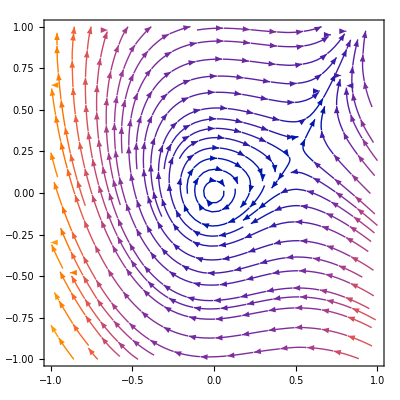

NDSolve::nderr: Error test failure at t == 24.6468; unable to continue.

NDSolve::nderr: Error test failure at t == 24.7702; unable to continue.

NDSolve::nderr: Error test failure at t == 24.8947; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

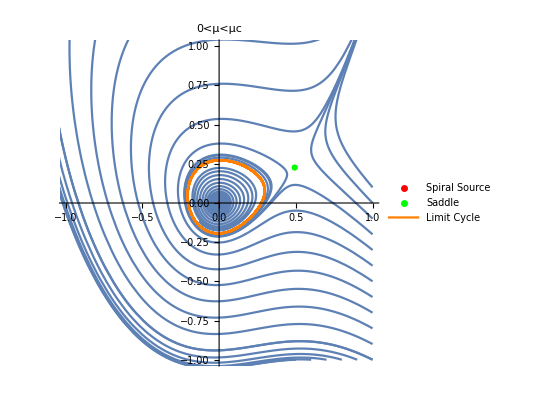

```mathematica
μ=μc/2
sol = Solve[f[x,y]==0 && g[x,y]==0, {x,y}]
StreamPlot[{f[x,y], g[x,y]}, {x,-1,1}, {y,-1,1}]
minx=-1; maxx=1; miny=-1;  maxy=1;
s[x0_,y0_]:=NDSolve[{x'[t]==μ*x[t]+y[t]-x[t]^2,y'[t]==-x[t]+μ*y[t]+2 x[t]^2,x[0]==x0, y[0]==y0},{x,y},{t,0,100}];
initialCondition=Join[Table[{minx,y},{y,miny,maxy,0.1}],Table[{maxx,y},{y,miny,maxy,0.1}],Table[{x,miny},{x,minx,maxx,0.1}],Table[{x,maxy},{x,minx,maxx,0.1}]];
Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/. s[initialCondition[[i,1]],initialCondition[[i,2]]]],{t,0,20}, PlotRange->{{minx,maxx},{miny,maxy}}],{i,Length[initialCondition]}], ListPlot[{{0,0}}, PlotStyle->{Red}, PlotMarkers->{Automatic, 6},PlotLegends->{"Spiral Source"}], ListPlot[{{sol[[2,1,2]],sol[[2,2,2]]}}, PlotStyle->{Green}, PlotMarkers->{Automatic, 6},PlotLegends->{"Saddle"}],
ParametricPlot[Evaluate[{x[t],y[t]}/. s[-0.2,0]],{t,0,100}, PlotRange->{{minx,maxx},{miny,maxy}},PlotStyle->{Orange},PlotLegends->{"Limit Cycle"}],
ParametricPlot[Evaluate[{x[t],y[t]}/. s[0.01,0.01]],{t,0,100}, PlotRange->{{minx,maxx},{miny,maxy}}],PlotLabel-> "0<μ<μc"]
```

0.066

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→0.,y→0.},{x→0.486136,y→0.204243}}

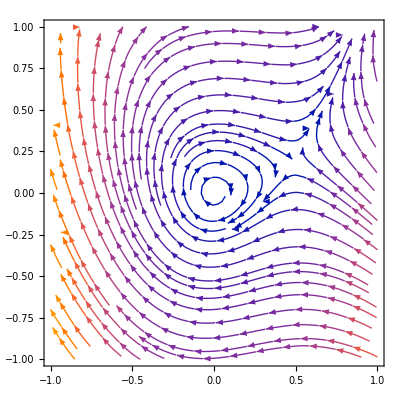

NDSolve::nderr: Error test failure at t == 24.1149; unable to continue.

NDSolve::nderr: Error test failure at t == 24.3761; unable to continue.

NDSolve::nderr: Error test failure at t == 24.442; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

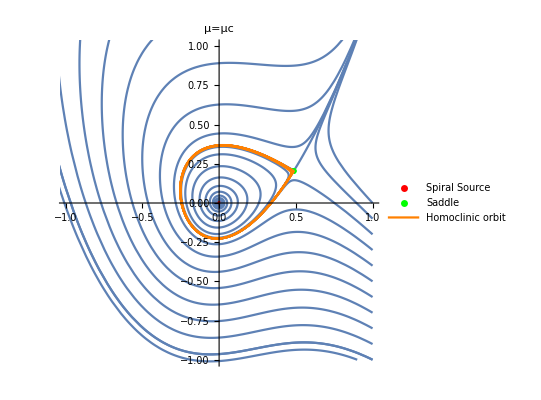

```mathematica
μ=μc
sol = Solve[f[x,y]==0 && g[x,y]==0, {x,y}]
StreamPlot[{f[x,y], g[x,y]}, {x,-1,1}, {y,-1,1}]
minx=-1; maxx=1; miny=-1;  maxy=1;
s[x0_,y0_]:=NDSolve[{x'[t]==μ*x[t]+y[t]-x[t]^2,y'[t]==-x[t]+μ*y[t]+2 x[t]^2,x[0]==x0, y[0]==y0},{x,y},{t,0,100}];
initialCondition=Join[Table[{minx,y},{y,miny,maxy,0.1}],Table[{maxx,y},{y,miny,maxy,0.1}],Table[{x,miny},{x,minx,maxx,0.1}],Table[{x,maxy},{x,minx,maxx,0.1}]];
Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/. s[initialCondition[[i,1]],initialCondition[[i,2]]]],{t,0,20}, PlotRange->{{minx,maxx},{miny,maxy}}],{i,Length[initialCondition]}], ListPlot[{{0,0}}, PlotStyle->{Red}, PlotMarkers->{Automatic, 6},PlotLegends->{"Spiral Source"}], ListPlot[{{sol[[2,1,2]],sol[[2,2,2]]}}, PlotStyle->{Green}, PlotMarkers->{Automatic, 6},PlotLegends->{"Saddle"}],
ParametricPlot[Evaluate[{x[t],y[t]}/. s[0.01,0.01]],{t,0,100}, PlotRange->{{minx,maxx},{miny,maxy}}],
ParametricPlot[Evaluate[{x[t],y[t]}/. s[0,-0.225]],{t,0,50}, PlotRange->{{minx,maxx},{miny,maxy}},PlotStyle->{Orange},PlotLegends->{"Homoclinic orbit"}],PlotLabel-> "μ=μc"]
```

1

{{x→0,y→0},{x→2/3,y→-2/9}}

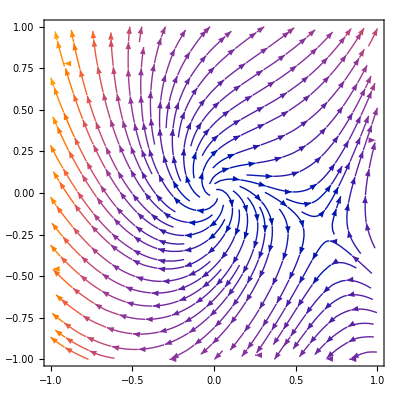

NDSolve::ndsz: At t == 3.24028, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 2.75686, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 2.50094, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

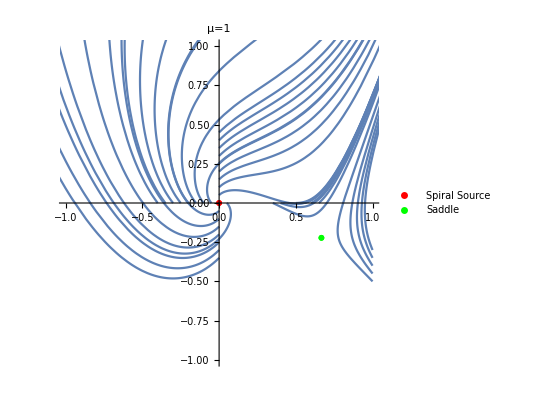

```mathematica
μ=1
sol = Solve[f[x,y]==0 && g[x,y]==0, {x,y}]
StreamPlot[{f[x,y], g[x,y]}, {x,-1,1}, {y,-1,1}]
minx=-1; maxx=1; miny=-1;  maxy=1;
s[x0_,y0_]:=NDSolve[{x'[t]==μ*x[t]+y[t]-x[t]^2,y'[t]==-x[t]+μ*y[t]+2 x[t]^2,x[0]==x0, y[0]==y0},{x,y},{t,0,10}];
initialCondition=Join[Table[{1,y},{y,0,miny,-0.05}],Table[{0,y},{y,miny,maxy,0.05}],Table[{x,0},{x,minx,maxx,0.05}]];
Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/. s[initialCondition[[i,1]],initialCondition[[i,2]]]],{t,0,20}, PlotRange->{{minx,maxx},{miny,maxy}}],{i,Length[initialCondition]}], ListPlot[{{0,0}}, PlotStyle->{Red}, PlotMarkers->{Automatic, 6},PlotLegends->{"Spiral Source"}], ListPlot[{{sol[[2,1,2]],sol[[2,2,2]]}}, PlotStyle->{Green}, PlotMarkers->{Automatic, 6},PlotLegends->{"Saddle"}],PlotLabel-> "μ=1"]
```

```mathematica
tConst = 0;
f=s[[1,1,2]];
g =s[[1,2,2]];
xStart = s[[1,1,2]][tMin];
yStart = s[[1,2,2]][tMin];
temp=FindRoot[f[t]+ g[t]==xStart+yStart,{t,tMin+tConst}];

xStart
s[[1,1,2]][temp[[1,2]]]
yStart
s[[1,2,2]][temp[[1,2]]]
tPeriod = Abs[tMin-temp[[1,2]]];
{Abs[μ-μc], tPeriod}
```

0.350527

0.350527

0.0186812

0.0186812

{0.006,0.}

1.62606-0.130313 x

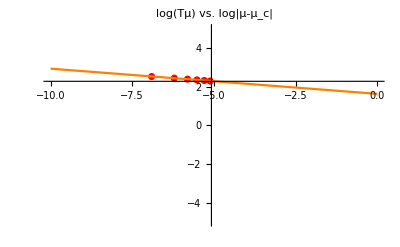

```mathematica
plotDataPeriodTime = {{0.006000000000000005,9.8624007122786},{0.0050000000000000044,10.13014722525466},{0.0040000000000000036,10.457176976655632}, {0.0030000000000000027,10.87749191550094},{0.0020000000000000018,11.46649270087542},{0.0010000000000000009,12.45832661710071}};
logPlotDataPeriodTime = Log[plotDataPeriodTime];
line =  Fit[logPlotDataPeriodTime,{1,x},x]
periodPlot = Show[ListPlot[logPlotDataPeriodTime,PlotStyle->Red],Plot[line,{x,-10,0},PlotStyle->Orange],PlotRange->{{-10,0},{-5,5}},PlotLabel->"log(Tμ) vs. log|μ-μ_c|"]
```